## Optimal Execution with Limit and Market Orders

## 8.2 Liquidation with Only Limit Orders

```mathematica
ω[t_,q_]:= ∑_(n=0)^q tλ^n/(n!)*ⅇ^(-κ*α*(q-n)^2)*(T-t)^n
ω[t_,q_]:=ⅇ^(-κ*α*q^2)/;t==T
ω[t_,q_]:=1/;q== 0
```

```mathematica
δ[t_,q_]:=1/κ*(1+Log[ω[t,q]/ω[t,q-1]])
(*
	Optimal Depth: Post LO @Price=S_t + δ 
*)
```

```mathematica
λ=50/60;
tλ=λ*ⅇ^-1;

κ=100.0;
T=60;
α=10^-3;
𝒩=5;
σ=0.01;
```

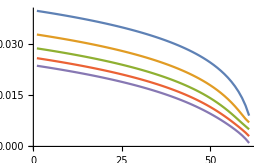

```mathematica
ListLinePlot@Table[Table[N@δ[t,q],{t,0,T}],{q,1,5}](*α-> 10^-3*)
```

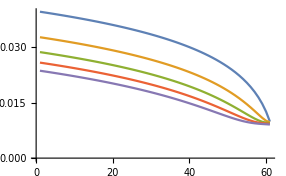

```mathematica
ListLinePlot@Table[Table[N@δ[t,q],{t,0,T}],{q,1,5}](*α-> 10^-4*)
```

#### Numerical Experiments

```mathematica
(*Price Dynamics*)
S0=30;
𝒫=TransformedProcess[S0+σ*(W[t]),{W\[Distributed]WienerProcess[]},t];
```

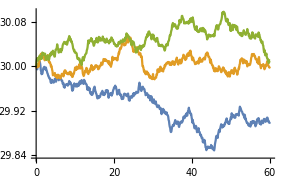
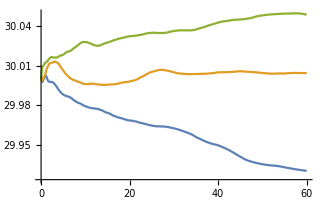

```mathematica
With[{data = RandomFunction[𝒫,{0,T,0.1},3]},
{ListLinePlot[data,PlotRange->All], ListLinePlot[TWAP[data]]}]
```

```mathematica
TWAP[price_]:=MovingMap[Mean,price,price["PathLength"],None]
```

```mathematica
TWAP[ RandomFunction[𝒫,{0,T,0.1},3]]
```

TemporalData[…]

```mathematica
Normal[dt][[1]]
```

{{0.,30.},{0.1,30.0002},{0.2,30.0051},{0.3,30.01},{0.4,30.0085},{0.5,30.014},{0.6,30.0124},{0.7,30.0132},{0.8,30.0107},{0.9,30.0144},{1.,30.01},{1.1,30.0102},{1.2,30.003},{1.3,30.0031},{1.4,30.0009},{1.5,30.0044},{1.6,30.0004},{1.7,30.008},{1.8,30.0109},{1.9,30.0067},{2.,30.0022},{2.1,30.0027},{2.2,30.0082},{2.3,30.0066},{2.4,30.0082},{2.5,30.0109},{2.6,30.0153},{2.7,30.0181},{2.8,30.0216},{2.9,30.0292},{3.,30.0281},{3.1,30.0272},{3.2,30.0267},{3.3,30.0342},{3.4,30.0374},{3.5,30.0404},{3.6,30.0368},{3.7,30.0343},{3.8,30.0315},{3.9,30.035},{4.,30.0361},{4.1,30.0364},{4.2,30.0326},{4.3,30.0324},{4.4,30.0313},{4.5,30.0313},{4.6,30.0351},{4.7,30.0339},{4.8,30.0359},{4.9,30.0344},{5.,30.0337},{5.1,30.0361},{5.2,30.0414},{5.3,30.0353},{5.4,30.0379},{5.5,30.0377},{5.6,30.0407},{5.7,30.0323},{5.8,30.0348},{5.9,30.0347},{6.,30.0361},{6.1,30.0338},{6.2,30.0318},{6.3,30.0315},{6.4,30.0325},{6.5,30.0274},{6.6,30.0286},{6.7,30.0258},{6.8,30.0294},{6.9,30.0348},{7.,30.0374},{7.1,30.0402},{7.2,30.0404},{7.3,30.0414},{7.4,30.0462},{7.5,30.0511},{7.6,30.0536},{7.7,30.052},{7.8,30.051},{7.9,30.0498},{8.,30.0506},{8.1,30.0515},{8.2,30.0499},{8.3,30.0579},{8.4,30.055},{8.5,30.0557},{8.6,30.0545},{8.7,30.0506},{8.8,30.0479},{8.9,30.0422},{9.,30.0397},{9.1,30.043},{9.2,30.0358},{9.3,30.0346},{9.4,30.0355},{9.5,30.0322},{9.6,30.0288},{9.7,30.0314},{9.8,30.0336},{9.9,30.0288},{10.,30.0247},{10.1,30.021},{10.2,30.0175},{10.3,30.0153},{10.4,30.0105},{10.5,30.0129},{10.6,30.018},{10.7,30.0126},{10.8,30.0123},{10.9,30.0095},{11.,30.0156},{11.1,30.0157},{11.2,30.0095},{11.3,30.0049},{11.4,30.004},{11.5,30.004},{11.6,30.0032},{11.7,30.0016},{11.8,29.9999},{11.9,29.9999},{12.,30.0018},{12.1,30.0042},{12.2,30.0039},{12.3,30.0017},{12.4,29.9995},{12.5,30.002},{12.6,29.9984},{12.7,29.9953},{12.8,29.9908},{12.9,29.9902},{13.,29.9906},{13.1,29.9914},{13.2,29.9962},{13.3,30.0028},{13.4,30.0049},{13.5,30.0059},{13.6,30.0072},{13.7,30.0054},{13.8,30.0087},{13.9,30.0129},{14.,30.0119},{14.1,30.0137},{14.2,30.0159},{14.3,30.0127},{14.4,30.0172},{14.5,30.0148},{14.6,30.0133},{14.7,30.0063},{14.8,30.0068},{14.9,30.007},{15.,30.0076},{15.1,30.0131},{15.2,30.016},{15.3,30.0185},{15.4,30.0203},{15.5,30.0214},{15.6,30.0211},{15.7,30.019},{15.8,30.022},{15.9,30.0221},{16.,30.0236},{16.1,30.0267},{16.2,30.0264},{16.3,30.0297},{16.4,30.0329},{16.5,30.0342},{16.6,30.0361},{16.7,30.0371},{16.8,30.0373},{16.9,30.038},{17.,30.038},{17.1,30.0334},{17.2,30.0288},{17.3,30.0285},{17.4,30.0285},{17.5,30.0248},{17.6,30.0215},{17.7,30.0219},{17.8,30.0189},{17.9,30.0174},{18.,30.0137},{18.1,30.008},{18.2,30.0071},{18.3,30.0104},{18.4,30.0076},{18.5,30.0065},{18.6,30.0092},{18.7,30.0112},{18.8,30.0068},{18.9,30.0086},{19.,30.0043},{19.1,29.9998},{19.2,30.0054},{19.3,30.0041},{19.4,30.0076},{19.5,30.0038},{19.6,30.0067},{19.7,30.0029},{19.8,30.0036},{19.9,30.007},{20.,30.0072},{20.1,30.0074},{20.2,30.0069},{20.3,30.005},{20.4,30.0061},{20.5,30.0094},{20.6,30.0107},{20.7,30.0086},{20.8,30.0132},{20.9,30.0155},{21.,30.0177},{21.1,30.0222},{21.2,30.0188},{21.3,30.0174},{21.4,30.0196},{21.5,30.0187},{21.6,30.0226},{21.7,30.0178},{21.8,30.0179},{21.9,30.0166},{22.,30.0142},{22.1,30.0141},{22.2,30.0155},{22.3,30.0112},{22.4,30.0119},{22.5,30.0121},{22.6,30.0144},{22.7,30.0153},{22.8,30.0114},{22.9,30.0072},{23.,30.0066},{23.1,30.0019},{23.2,30.0054},{23.3,30.0076},{23.4,30.0089},{23.5,30.0098},{23.6,30.0161},{23.7,30.0159},{23.8,30.0174},{23.9,30.0183},{24.,30.0185},{24.1,30.0224},{24.2,30.0245},{24.3,30.0263},{24.4,30.0282},{24.5,30.0264},{24.6,30.0302},{24.7,30.0248},{24.8,30.028},{24.9,30.0306},{25.,30.0282},{25.1,30.0286},{25.2,30.0267},{25.3,30.0298},{25.4,30.0295},{25.5,30.0293},{25.6,30.0356},{25.7,30.0362},{25.8,30.0399},{25.9,30.0383},{26.,30.037},{26.1,30.0389},{26.2,30.0375},{26.3,30.0425},{26.4,30.0413},{26.5,30.0419},{26.6,30.0422},{26.7,30.0437},{26.8,30.0524},{26.9,30.0557},{27.,30.0556},{27.1,30.0571},{27.2,30.0579},{27.3,30.0542},{27.4,30.06},{27.5,30.0621},{27.6,30.0584},{27.7,30.0561},{27.8,30.0564},{27.9,30.0545},{28.,30.0489},{28.1,30.0451},{28.2,30.0454},{28.3,30.0498},{28.4,30.0492},{28.5,30.0479},{28.6,30.0451},{28.7,30.0452},{28.8,30.0459},{28.9,30.0425},{29.,30.0438},{29.1,30.0396},{29.2,30.0342},{29.3,30.0375},{29.4,30.0364},{29.5,30.0396},{29.6,30.0322},{29.7,30.0302},{29.8,30.0266},{29.9,30.025},{30.,30.027},{30.1,30.0291},{30.2,30.0307},{30.3,30.0354},{30.4,30.0351},{30.5,30.0353},{30.6,30.0354},{30.7,30.0386},{30.8,30.0429},{30.9,30.0419},{31.,30.0467},{31.1,30.0365},{31.2,30.0311},{31.3,30.0377},{31.4,30.0409},{31.5,30.0409},{31.6,30.0385},{31.7,30.0345},{31.8,30.0384},{31.9,30.0396},{32.,30.04},{32.1,30.0372},{32.2,30.0342},{32.3,30.0342},{32.4,30.0366},{32.5,30.0414},{32.6,30.0396},{32.7,30.0462},{32.8,30.0478},{32.9,30.0494},{33.,30.045},{33.1,30.0445},{33.2,30.0473},{33.3,30.0497},{33.4,30.0475},{33.5,30.0509},{33.6,30.0528},{33.7,30.0542},{33.8,30.0555},{33.9,30.0578},{34.,30.0552},{34.1,30.0497},{34.2,30.0504},{34.3,30.0461},{34.4,30.0459},{34.5,30.045},{34.6,30.0472},{34.7,30.0418},{34.8,30.0451},{34.9,30.046},{35.,30.0484},{35.1,30.0418},{35.2,30.0374},{35.3,30.0353},{35.4,30.0333},{35.5,30.0385},{35.6,30.0422},{35.7,30.0378},{35.8,30.0395},{35.9,30.0401},{36.,30.0398},{36.1,30.0389},{36.2,30.0391},{36.3,30.0338},{36.4,30.0352},{36.5,30.0317},{36.6,30.0239},{36.7,30.0242},{36.8,30.0254},{36.9,30.0281},{37.,30.0272},{37.1,30.0255},{37.2,30.0229},{37.3,30.018},{37.4,30.0196},{37.5,30.0181},{37.6,30.0185},{37.7,30.0164},{37.8,30.0183},{37.9,30.0166},{38.,30.0211},{38.1,30.0202},{38.2,30.018},{38.3,30.0126},{38.4,30.0096},{38.5,30.012},{38.6,30.0118},{38.7,30.0134},{38.8,30.0139},{38.9,30.0168},{39.,30.0176},{39.1,30.0185},{39.2,30.0198},{39.3,30.0212},{39.4,30.0145},{39.5,30.0113},{39.6,30.0068},{39.7,30.006},{39.8,30.0049},{39.9,29.9978},{40.,29.9974},{40.1,30.0038},{40.2,30.0093},{40.3,30.0037},{40.4,29.9976},{40.5,29.9985},{40.6,29.9981},{40.7,29.9958},{40.8,29.9987},{40.9,29.9967},{41.,29.9933},{41.1,29.9896},{41.2,29.9889},{41.3,29.9842},{41.4,29.9907},{41.5,29.9932},{41.6,29.9946},{41.7,30.0006},{41.8,29.9943},{41.9,29.9963},{42.,29.9955},{42.1,29.9994},{42.2,30.0024},{42.3,30.0034},{42.4,30.0003},{42.5,30.0002},{42.6,30.003},{42.7,30.0016},{42.8,30.0007},{42.9,30.0031},{43.,30.0026},{43.1,30.},{43.2,30.0012},{43.3,30.0013},{43.4,30.003},{43.5,30.0072},{43.6,30.0094},{43.7,30.0141},{43.8,30.0183},{43.9,30.0154},{44.,30.0142},{44.1,30.0131},{44.2,30.0104},{44.3,30.0097},{44.4,30.0063},{44.5,30.0023},{44.6,30.0002},{44.7,30.0018},{44.8,30.0065},{44.9,30.0089},{45.,30.0124},{45.1,30.0121},{45.2,30.0143},{45.3,30.0195},{45.4,30.018},{45.5,30.0162},{45.6,30.0172},{45.7,30.0163},{45.8,30.0169},{45.9,30.0155},{46.,30.0178},{46.1,30.0177},{46.2,30.0201},{46.3,30.0219},{46.4,30.0187},{46.5,30.0205},{46.6,30.0205},{46.7,30.0193},{46.8,30.0141},{46.9,30.0179},{47.,30.0168},{47.1,30.0215},{47.2,30.0259},{47.3,30.0265},{47.4,30.0286},{47.5,30.0246},{47.6,30.0251},{47.7,30.0232},{47.8,30.0288},{47.9,30.0209},{48.,30.0222},{48.1,30.0296},{48.2,30.0265},{48.3,30.0303},{48.4,30.031},{48.5,30.032},{48.6,30.0288},{48.7,30.03},{48.8,30.0255},{48.9,30.0207},{49.,30.0165},{49.1,30.0188},{49.2,30.0217},{49.3,30.0179},{49.4,30.0152},{49.5,30.01},{49.6,30.0118},{49.7,30.0115},{49.8,30.0111},{49.9,30.0136},{50.,30.0135},{50.1,30.0069},{50.2,30.0026},{50.3,30.0059},{50.4,30.0106},{50.5,30.0091},{50.6,30.0055},{50.7,30.0054},{50.8,30.0075},{50.9,30.0057},{51.,30.0016},{51.1,30.0003},{51.2,30.0024},{51.3,30.0024},{51.4,30.0004},{51.5,30.0068},{51.6,30.0067},{51.7,30.0044},{51.8,30.0003},{51.9,30.003},{52.,30.0086},{52.1,30.0116},{52.2,30.0102},{52.3,30.012},{52.4,30.0129},{52.5,30.0115},{52.6,30.0095},{52.7,30.009},{52.8,30.0083},{52.9,30.0075},{53.,30.0093},{53.1,30.0126},{53.2,30.0108},{53.3,30.0121},{53.4,30.0094},{53.5,30.0119},{53.6,30.01},{53.7,30.0146},{53.8,30.0134},{53.9,30.0097},{54.,30.0121},{54.1,30.012},{54.2,30.0042},{54.3,30.0017},{54.4,30.0061},{54.5,30.0078},{54.6,30.0014},{54.7,30.0014},{54.8,30.0047},{54.9,30.0066},{55.,30.0029},{55.1,29.9994},{55.2,30.0036},{55.3,30.0029},{55.4,29.9972},{55.5,29.9993},{55.6,29.9955},{55.7,29.9923},{55.8,29.9913},{55.9,29.9882},{56.,29.9877},{56.1,29.9848},{56.2,29.9763},{56.3,29.9755},{56.4,29.9744},{56.5,29.9713},{56.6,29.9718},{56.7,29.9779},{56.8,29.9773},{56.9,29.9785},{57.,29.9798},{57.1,29.9797},{57.2,29.9717},{57.3,29.977},{57.4,29.9697},{57.5,29.9708},{57.6,29.978},{57.7,29.983},{57.8,29.9863},{57.9,29.9899},{58.,29.9867},{58.1,29.984},{58.2,29.9876},{58.3,29.9893},{58.4,29.9919},{58.5,29.9911},{58.6,29.9873},{58.7,29.989},{58.8,29.9925},{58.9,29.9938},{59.,29.9924},{59.1,29.9902},{59.2,29.9888},{59.3,29.9935},{59.4,29.9915},{59.5,29.9943},{59.6,29.9882},{59.7,29.9895},{59.8,29.9878},{59.9,29.9869},{60.,29.9895}}

```mathematica
fillProb[δ_]:=ⅇ^(-κ*δ)
```

```mathematica
fillProb[0.01]
```

0.367879

```mathematica
Table[RandomVariate@BernoulliDistribution[0.36],10]
```

{0,1,1,0,1,1,1,1,0,0}

```mathematica
backTest[price_]:=Module[
{left=𝒩,
tb=Normal[price][[1]],
depth,
time,
mPrice,
postPrice,
fillQ,
depthHis={},
inventoryHis={},
trdHis={}},
Do[{
time=tb[[idx]][[1]];
mPrice=tb[[idx]][[2]];
depth=δ[time,left];
AppendTo[depthHis,{time,depth}];
postPrice=mPrice+depth;
fillQ=RandomVariate[BernoulliDistribution[fillProb[depth]]];
If[fillQ==1,AppendTo[trdHis,{time,postPrice}]];
left-=fillQ;
AppendTo[inventoryHis,{time,left}];
};If[left==0,Break[]],{idx,1,Length@tb}];
Association["depth"-> TemporalData[depthHis],"inventory"-> TemporalData[inventoryHis],"trade"-> TemporalData[trdHis]]
]
```

```mathematica
res=backTest[dt]
```

<|depth→TemporalData[…],inventory→TemporalData[…],trade→TemporalData[…]|>

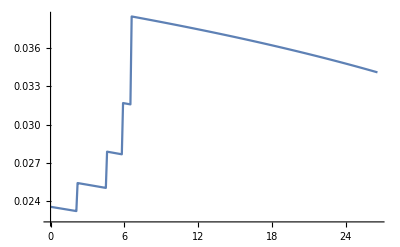

```mathematica
ListLinePlot[res["depth"]]
```

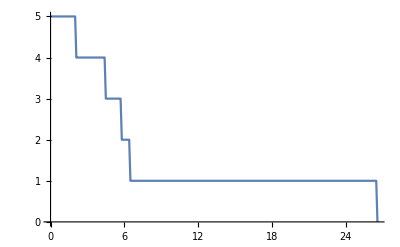

```mathematica
ListLinePlot[res["inventory"]]
```

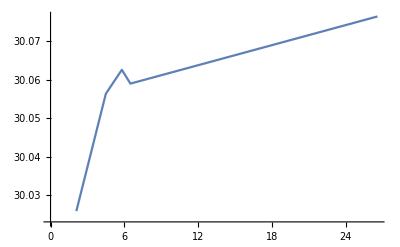

```mathematica
ListLinePlot[res["trade"]]
```

```mathematica
Mean@res["trade"]
```

30.056

```mathematica
Mean@dt
```

30.0186